```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 18 Kb

{Utilities`CleanSlate`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,Parallel`Debug`Perfmon`,Parallel`Debug`,System`,Global`}

```mathematica
Clear[q]
q = θ[t]
```

θ[t]

```mathematica
D[q, t]
```

θ'[t]

```mathematica
Clear[r]
r = { 1/2 l Cos[θ[t]] , 1/2 l Sin[θ[t]] , -1/2 l Cos[θ[t]] , 1/2 l Sin[θ[t]] }
```

{1/2 l Cos[θ[t]],1/2 l Sin[θ[t]],-1/2 l Cos[θ[t]],1/2 l Sin[θ[t]]}

```mathematica
D[r, t]
```

{-1/2 l Sin[θ[t]] θ'[t],1/2 l Cos[θ[t]] θ'[t],1/2 l Sin[θ[t]] θ'[t],1/2 l Cos[θ[t]] θ'[t]}

```mathematica
D[r, t] . D[r, t]
```

1/2 l^2 Cos[θ[t]]^2 θ'[t]^2+1/2 l^2 Sin[θ[t]]^2 θ'[t]^2

```mathematica
D[r, t] . D[r, t]   // Expand  // Simplify
```

1/2 l^2 θ'[t]^2

```mathematica
1/2( 2 ) (1/12 m l^2 θ'[t]^2)
```

1/12 l^2 m θ'[t]^2

```mathematica
Clear[T]
T = 1/2 m ( D[r, t] . D[r, t]   // Expand  // Simplify  ) + 1/2( 2 ) (1/12 m l^2 θ'[t]^2)
```

1/3 l^2 m θ'[t]^2

```mathematica
Clear[V] 
V =  m g l Sin[θ[t] ]
```

g l m Sin[θ[t]]

```mathematica
Clear[ℒ]
ℒ = T - V
```

-g l m Sin[θ[t]]+1/3 l^2 m θ'[t]^2

```mathematica
D[ D[ ℒ , D[q, t]], t]- D[ ℒ , q ]
```

g l m Cos[θ[t]]+2/3 l^2 m θ''[t]

```mathematica
Clear[eqs]
eqs = EulerEquations[ ℒ , q , t ]
```

-1/3 l m (3 g Cos[θ[t]]+2 l θ''[t])==0

```mathematica
Clear[ics]
ics = { 
θ[0] == π/3,
θ'[0] == 0 
};
ics // TableForm
```

θ[0]==π/3
θ'[0]==0

```mathematica
Clear[parameters]
parameters = { 
m-> 20 , 
g-> 9.8,
l-> 2 } ;
parameters // TableForm
```

m→20
g→9.8
l→2

```mathematica
eqs //. parameters
```

-40/3 (29.4 Cos[θ[t]]+4 θ''[t])==0

```mathematica
Clear[solution]
solution[t_] = First[NDSolve[ Union[{eqs //. parameters} , ics ] , q, { t, 0, 10 } ]]
```

{θ[t]→InterpolatingFunction[…][t]}

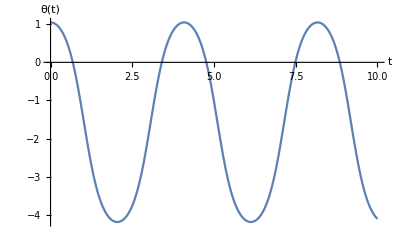

```mathematica
Plot[ Evaluate[ q /. solution[t]] , { t,0,10} , AxesLabel-> { t , q }  ]
```

```mathematica
Solve[ Evaluate[(  q /. solution[t] ) == 0  ]  , t ]   (* Compare this with part b *)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0.680677}}

```mathematica
solution[t]
solution[t][[1]]
solution[t][[1,2]]
```

{θ[t]→InterpolatingFunction[…][t]}

θ[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

```mathematica
Animate[
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t, 0, tmax } , AxesLabel-> { q , D[q, t] } ]   , { tmax , 0.1 , 10 } ]
```